```mathematica
Gs={{(s+4)/((s+1)(s+5)), 1/(5s+1)},{(s+1)/(s^2+10s+100),2/(2s+1)}}
```

{{(4+s)/((1+s) (5+s)),1/(1+5 s)},{(1+s)/(100+10 s+s^2),2/(1+2 s)}}

```mathematica
MatrixForm[Gs]
```

((4+s)/((1+s) (5+s)) | 1/(1+5 s)
(1+s)/(100+10 s+s^2) | 2/(1+2 s))

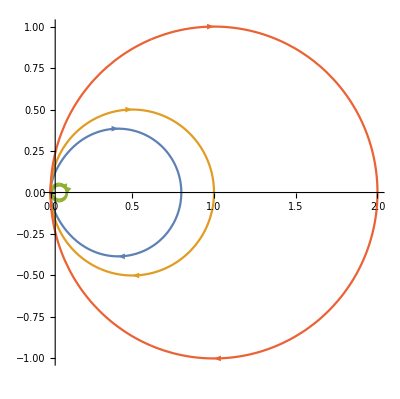

```mathematica
NyquistPlot[Gs]
```

```mathematica
Kinv=Gs/.s->0
```

{{4/5,1},{1/100,2}}

```mathematica
Qinv=Simplify[Kinv.Inverse[Gs]]
```

{{-((1+s) (5+s) (1+5 s) (-795-65 s+2 s^2))/(5 (795+4259 s+1399 s^2+127 s^3+8 s^4)),(3 s (1+2 s) (27+7 s) (100+10 s+s^2))/(5 (795+4259 s+1399 s^2+127 s^3+8 s^4))},{-(s (1+s) (5+s) (1+5 s) (290+199 s))/(50 (795+4259 s+1399 s^2+127 s^3+8 s^4)),(3 (1+2 s) (100+10 s+s^2) (265+1398 s+333 s^2))/(100 (795+4259 s+1399 s^2+127 s^3+8 s^4))}}

```mathematica
Gjw=Gs/.s->(w I);
```

```mathematica
M=Abs[Gjw];
```

```mathematica
Omega={{M[[1,1]],0},{0,M[[2,2]]}};
```

```mathematica
Mnorm=Inverse[Omega].M;
```

```mathematica
li=Eigenvalues[Mnorm];
```

```mathematica
lpf=li[[2]];
```

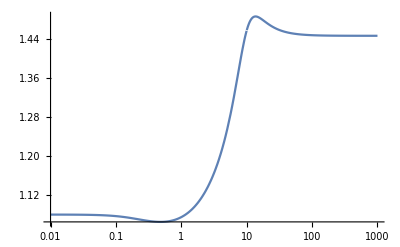

```mathematica
LogLinearPlot[lpf,{w,0.01,1000}]
```